## First the basics

```mathematica
Table[allGraphs5[k,"atleast"]=0,{k,Keys[allGraphs5]}];
```

```mathematica
Table[If[ToString[allGraphs5[k,"comp"]]=="Greater",allGraphs5[k,"atleast"]=1],{k,Keys[allGraphs5]}];
```

```mathematica
Table[allGraphs5[k,"comp"]=Equal,{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]
```

{Equal,Equal,Equal,Equal,Equal}

```mathematica
Table[allGraphs5[k,"comp"]=Greater,{k,{quad1Key,quad2Key,quad3Key,quad4Key,quad5Key}}]
```

{Greater,Greater,Greater,Greater,Greater}

```mathematica
Propagate[]:=Block[{newValue,current,left,right,new,changes=0},
Table[
Table[
current=allGraphs5[k,"atleast"];
left=allGraphs5[c[[1]],"atleast"];
right=allGraphs5[c[[2]],"atleast"];
new=Max[current,left+right];
If[new≠current,
(*Print["Changing " ,k , " From " , current , " To ",new];*)
allGraphs5[k,"atleast"]=new;
changes++
]
,{c,allGraphs5[k,"children"]}
]
,{k,Keys[allGraphs5]}
];
Print[changes]
]
```

```mathematica
Propagate[]
```

1928

```mathematica
Propagate[]
```

464

```mathematica
Propagate[]
```

0

```mathematica
Sort[Tally[Table[allGraphs5[k,"comp"],{k,allGraphs5AtomKeys}]]]
```

{{Equal,6},{Greater,26},{GreaterEqual,20}}

```mathematica
Tally[Table[allGraphs5[k,"atleast"]
,{k,Keys[allGraphs5]}]]//Sort
```

{{0,51},{1,226},{2,305},{3,270},{4,240},{5,167},{6,180},{7,55},{8,130},{9,50},{10,50},{11,25},{12,50},{13,15},{14,25},{15,10},{17,15},{18,15},{20,5},{23,5},{26,5},{36,1}}

```mathematica
Summarize[]:=Block[{newValue,current,left,right,new},
Monitor[
Select[
Flatten[
Table[
Table[
current=allGraphs5[k,"atleast"];
left=allGraphs5[c[[1]],"atleast"];
right=allGraphs5[c[[2]],"atleast"];
new=left+right;
If[new≠current,
Flatten[{current-new,current,left,right,k,c}],
{}
]
,{c,allGraphs5[k,"children"]}
]
,{k,Keys[allGraphs5]}
],
1],
#≠{}&
],
{k,c}
]
]
```

```mathematica
t=Summarize[]
```

{{2,18,12,4,26244,26325,28593},{2,18,13,3,26244,26271,27027},{2,14,8,4,28431,28512,28593},{3,14,9,2,28431,28458,29214},{1,14,10,3,28431,28434,29166},{1,10,6,3,29160,29241,29322},{3,10,5,2,29160,29187,29214},{1,10,6,3,29160,29163,29166},{1,6,4,1,29403,29484,29574},{2,6,3,1,29403,29430,29460},{1,4,2,1,29484,29511,29542},{1,2,1,0,29502,29529,29560},{1,1,0,0,29506,29533,29560},{1,2,0,1,29487,29514,29542},{1,2,0,1,29488,29515,29542},{1,3,1,1,29485,29512,29542},1729,{1,6,4,1,63,2250,10998},{1,4,2,1,72,8820,17568},{1,4,2,1,72,8820,17568},{2,18,12,4,12,2199,10947},{2,18,13,3,12,93,417},{2,10,7,1,13,2200,11677},{2,10,7,1,13,94,445},{2,5,3,0,16,2203,11680},{2,5,3,0,16,97,448},{2,26,18,6,3,2190,4377},{2,26,18,6,3,84,165},{2,18,13,3,4,2191,5107},{2,18,12,4,4,85,193},{2,10,6,2,6,2193,4380},{2,10,6,2,6,87,168}}
 |  |  |  |

```mathematica
Max[Map[First,t]]
```

3

```mathematica
Select[t,#[[1]]==4&]
```

{}

```mathematica
ShowGraph2[k_]:=Labeled[Tooltip[ShowGraph[allGraphs5,k],allGraphs5[k,"compwhy"]],Style[allGraphs5[k,"atleast"],Blue],Top]
```

```mathematica
Table[{ShowGraph2[0],ShowGraph2[k[[1]]],ShowGraph2[k[[2]]]},{k,allGraphs5[0,"children"]}]
```

{{-Graphics-036,-Graphics-1968323,-Graphics-3936613},{-Graphics-036,-Graphics-656126,-Graphics-1312210},{-Graphics-036,-Graphics-218726,-Graphics-437410},{-Graphics-036,-Graphics-72923,-Graphics-145813},{-Graphics-036,-Graphics-24323,-Graphics-48613},{-Graphics-036,-Graphics-8126,-Graphics-16210},{-Graphics-036,-Graphics-2726,-Graphics-5410},{-Graphics-036,-Graphics-923,-Graphics-1813},{-Graphics-036,-Graphics-326,-Graphics-610},{-Graphics-036,-Graphics-123,-Graphics-213}}

```mathematica
rep5=Table[allGraphs5[k,"colofour"]->ShowGraph2[k],{k,allGraphs5AtomKeys}]
```

{v1x2x3x4x5→-Graphics-295240,v1x2x3x45→-Graphics-295250,v1x2x35x4→-Graphics-295271,v1x2x34x5→-Graphics-295330,v1x2x345→-Graphics-295371,v1x25x3x4→-Graphics-295511,v1x25x34→-Graphics-295600,v1x24x3x5→-Graphics-296051,v1x24x35→-Graphics-296080,v1x245x3→-Graphics-296330,v1x23x4x5→-Graphics-297670,v1x23x45→-Graphics-297681,v1x235x4→-Graphics-297970,v1x234x5→-Graphics-298571,v1x2345→-Graphics-298881,v15x2x3x4→-Graphics-302530,v15x2x34→-Graphics-302621,v15x24x3→-Graphics-303340,v15x23x4→-Graphics-304961,v15x234→-Graphics-305861,v14x2x3x5→-Graphics-317111,v14x2x35→-Graphics-317140,v14x25x3→-Graphics-317380,v14x23x5→-Graphics-319540,v14x235→-Graphics-319840,v145x2x3→-Graphics-324411,v145x23→-Graphics-326841,v13x2x4x5→-Graphics-360851,v13x2x45→-Graphics-360860,v13x25x4→-Graphics-361120,v13x24x5→-Graphics-361660,v13x245→-Graphics-361940,v135x2x4→-Graphics-368170,v135x24→-Graphics-368980,v134x2x5→-Graphics-382810,v134x25→-Graphics-383080,v1345x2→-Graphics-390141,v12x3x4x5→-Graphics-492070,v12x3x45→-Graphics-492081,v12x35x4→-Graphics-492100,v12x34x5→-Graphics-492161,v12x345→-Graphics-492201,v125x3x4→-Graphics-499631,v125x34→-Graphics-499721,v124x3x5→-Graphics-514750,v124x35→-Graphics-514780,v1245x3→-Graphics-522321,v123x4x5→-Graphics-560111,v123x45→-Graphics-560121,v1235x4→-Graphics-567701,v1234x5→-Graphics-582881,v12345→-Graphics-590481}

```mathematica
allGraphs5[0,"colofour"]/.rep5
```

-Graphics-590481+-Graphics-582881+-Graphics-567701+-Graphics-560121+-Graphics-522321+-Graphics-499721+-Graphics-492201+-Graphics-514780+-Graphics-390141+-Graphics-326841+-Graphics-305861+-Graphics-298881+-Graphics-319840+-Graphics-368980+-Graphics-361940+-Graphics-383080+-Graphics-560111+-Graphics-514750+-Graphics-492161+-Graphics-499631+-Graphics-492100+-Graphics-492081+-Graphics-382810+-Graphics-319540+-Graphics-298571+-Graphics-361660+-Graphics-368170+-Graphics-304961+-Graphics-297970+-Graphics-361120+-Graphics-360860+-Graphics-297681+-Graphics-324411+-Graphics-303340+-Graphics-296330+-Graphics-317380+-Graphics-302621+-Graphics-295600+-Graphics-295371+-Graphics-317140+-Graphics-296080+-Graphics-492070+-Graphics-360851+-Graphics-297670+-Graphics-317111+-Graphics-296051+-Graphics-295330+-Graphics-302530+-Graphics-295511+-Graphics-295250+-Graphics-295271+-Graphics-295240

```mathematica
Equals[]:=Block[{newValue,current,left,right,new,changes=0,results={}},
Table[
Table[
current=allGraphs5[k,"atleast"];
left=allGraphs5[c[[1]],"atleast"];
right=allGraphs5[c[[2]],"atleast"];
new=Max[left+right];
If[new==current,
(*Print["Equal " ,k , " From " , current , " To ",new," graph ", k, " children ",c ];*)
AppendTo[results,k];
changes++
]
,{c,allGraphs5[k,"children"]}
]
,{k,Keys[allGraphs5]}
];
Print[changes];
Sort[DeleteDuplicates[results]]
]
```

```mathematica
direct=Equals[];
```

7080

```mathematica
Length[%480]
```

1

```mathematica
1813+52
```

1865

```mathematica
Length[Table[{ShowGraph2[k],allGraphs5[k,"colofour"]/.rep5},{k,Select[Keys[allGraphs5],!MemberQ[direct,#]&&!MemberQ[allGraphs5AtomKeys,#]&]}]]
```

20

```mathematica
TableForm[Table[{ShowGraph2[k],allGraphs5[k,"colofour"]/.rep5},{k,Select[Keys[allGraphs5],!MemberQ[direct,#]&&!MemberQ[allGraphs5AtomKeys,#]&]}]]
```

-Graphics-295061 | -Graphics-295600+-Graphics-295330
-Graphics-294171 | -Graphics-296330+-Graphics-295250
-Graphics-297371 | -Graphics-297970+-Graphics-297670
-Graphics-301721 | -Graphics-303340+-Graphics-302530
-Graphics-319241 | -Graphics-319840+-Graphics-319540
-Graphics-275801 | -Graphics-319540+-Graphics-297670
-Graphics-276101 | -Graphics-319840+-Graphics-297970
-Graphics-359781 | -Graphics-361940+-Graphics-360860
-Graphics-367361 | -Graphics-368980+-Graphics-368170
-Graphics-382541 | -Graphics-383080+-Graphics-382810
-Graphics-229641 | -Graphics-360860+-Graphics-295250
-Graphics-230721 | -Graphics-361940+-Graphics-296330
-Graphics-236891 | -Graphics-368170+-Graphics-302530
-Graphics-237701 | -Graphics-368980+-Graphics-303340
-Graphics-207851 | -Graphics-382810+-Graphics-295330
-Graphics-208121 | -Graphics-383080+-Graphics-295600
-Graphics-492041 | -Graphics-492100+-Graphics-492070
-Graphics-514721 | -Graphics-514780+-Graphics-514750
-Graphics-469391 | -Graphics-514750+-Graphics-492070
-Graphics-469421 | -Graphics-514780+-Graphics-492100

```mathematica
ShowGraph2[alfa1Key]
```

-Graphics-361660

```mathematica
34*24
```

816

## Now for five and real colofours

```mathematica
MyColors=Association[];
```

```mathematica
MyColors[Greater]=Green;MyColors[GreaterEqual]=Orange;MyColors[Equal]=Red;MyColors
```

<|Greater→RGBColor[0, 1, 0],GreaterEqual→RGBColor[1, 0.5, 0],Equal→RGBColor[1, 0, 0]|>

```mathematica
ChangeSYmbol[s_]:=Symbol["n"<>StringDrop[SymbolName[s],1]]
```

```mathematica
vertexLabels=Monitor[Table[ChangeSYmbol[allGraphs5[k,"colofourrealnull"]]-> Tooltip[Style[Rotate[allGraphs5[k,"atleast"],Pi/4],Red,Bold,14],Labeled[ShowGraph[allGraphs5,k],allGraphs5[k,"compwhy"]]],{k,Sort[allGraphs5NullAtomKeys]}],PadLeft[IntegerDigits[k,3],15]]
```

{n1x2x3x4x5→36,n1x2x3x45→13,n1x2x35x4→10,n1x2x34x5→13,n1x2x345→5,n1x25x3x4→10,n1x25x34→4,n1x24x3x5→10,n1x24x35→2,n1x245x3→4,n1x23x4x5→13,n1x23x45→5,n1x235x4→4,n1x234x5→5,n1x2345→2,n15x2x3x4→13,n15x2x34→5,n15x24x3→4,n15x23x4→5,n15x234→2,n14x2x3x5→10,n14x2x35→2,n14x25x3→2,n14x23x5→4,n14x235→1,n145x2x3→5,n145x23→2,n13x2x4x5→10,n13x2x45→4,n13x25x4→2,n13x24x5→2,n13x245→1,n135x2x4→4,n135x24→1,n134x2x5→4,n134x25→1,n1345x2→2,n12x3x4x5→13,n12x3x45→5,n12x35x4→4,n12x34x5→5,n12x345→2,n125x3x4→5,n125x34→2,n124x3x5→4,n124x35→1,n1245x3→2,n123x4x5→5,n123x45→2,n1235x4→2,n1234x5→2,n12345→1}

```mathematica
vertexStyle=Monitor[Table[ChangeSYmbol[allGraphs5[k,"colofourrealnull"]]-> MyColors[allGraphs5[k,"comp"]],{k,Sort[allGraphs5NullAtomKeys]}],PadLeft[IntegerDigits[k,3],15]]
```

{n1x2x3x4x5→RGBColor[0, 1, 0],n1x2x3x45→RGBColor[0, 1, 0],n1x2x35x4→RGBColor[0, 1, 0],n1x2x34x5→RGBColor[0, 1, 0],n1x2x345→RGBColor[0, 1, 0],n1x25x3x4→RGBColor[0, 1, 0],n1x25x34→RGBColor[0, 1, 0],n1x24x3x5→RGBColor[0, 1, 0],n1x24x35→RGBColor[0, 1, 0],n1x245x3→RGBColor[0, 1, 0],n1x23x4x5→RGBColor[0, 1, 0],n1x23x45→RGBColor[0, 1, 0],n1x235x4→RGBColor[0, 1, 0],n1x234x5→RGBColor[0, 1, 0],n1x2345→RGBColor[0, 1, 0],n15x2x3x4→RGBColor[0, 1, 0],n15x2x34→RGBColor[0, 1, 0],n15x24x3→RGBColor[0, 1, 0],n15x23x4→RGBColor[0, 1, 0],n15x234→RGBColor[0, 1, 0],n14x2x3x5→RGBColor[0, 1, 0],n14x2x35→RGBColor[0, 1, 0],n14x25x3→RGBColor[0, 1, 0],n14x23x5→RGBColor[0, 1, 0],n14x235→RGBColor[0, 1, 0],n145x2x3→RGBColor[0, 1, 0],n145x23→RGBColor[0, 1, 0],n13x2x4x5→RGBColor[0, 1, 0],n13x2x45→RGBColor[0, 1, 0],n13x25x4→RGBColor[0, 1, 0],n13x24x5→RGBColor[0, 1, 0],n13x245→RGBColor[0, 1, 0],n135x2x4→RGBColor[0, 1, 0],n135x24→RGBColor[0, 1, 0],n134x2x5→RGBColor[0, 1, 0],n134x25→RGBColor[0, 1, 0],n1345x2→RGBColor[0, 1, 0],n12x3x4x5→RGBColor[0, 1, 0],n12x3x45→RGBColor[0, 1, 0],n12x35x4→RGBColor[0, 1, 0],n12x34x5→RGBColor[0, 1, 0],n12x345→RGBColor[0, 1, 0],n125x3x4→RGBColor[0, 1, 0],n125x34→RGBColor[0, 1, 0],n124x3x5→RGBColor[0, 1, 0],n124x35→RGBColor[0, 1, 0],n1245x3→RGBColor[0, 1, 0],n123x4x5→RGBColor[0, 1, 0],n123x45→RGBColor[0, 1, 0],n1235x4→RGBColor[0, 1, 0],n1234x5→RGBColor[0, 1, 0],n12345→RGBColor[0, 1, 0]}

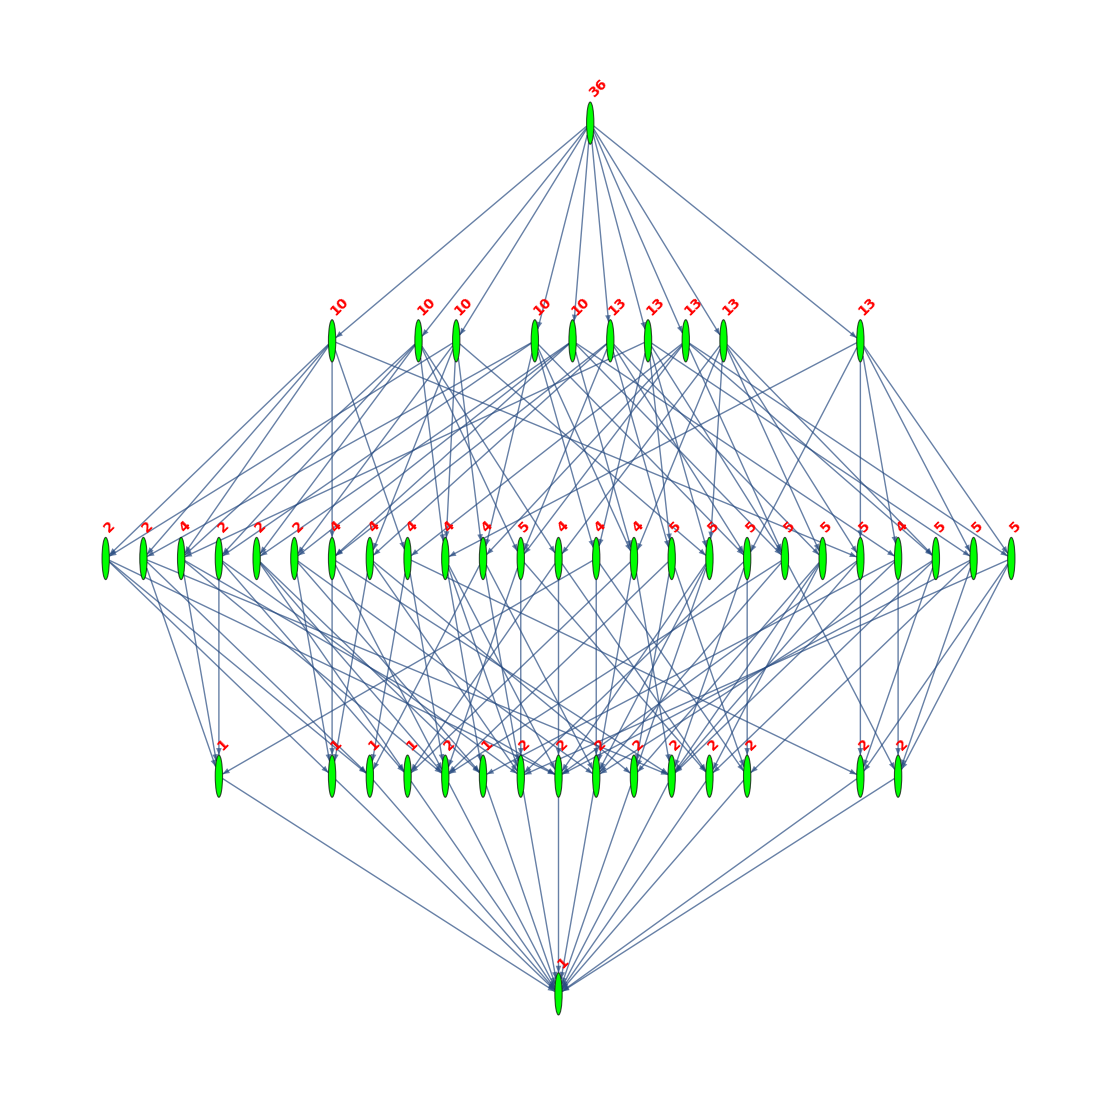

```mathematica
gr=Graph[EdgeList[MobiusGraph5[K5Key,allGraphs5]],VertexLabels->vertexLabels,GraphLayout->"LayeredDigraphEmbedding", VertexStyle->vertexStyle,AspectRatio->1]
```

```mathematica
repEmpty=Monitor[Table[ChangeSYmbol[allGraphs5[k,"colofourrealnull"]]-> allGraphs5[k,"atleast"],{k,Sort[allGraphs5NullAtomKeys]}],PadLeft[IntegerDigits[k,3],15]]
```

{n1x2x3x4x5→36,n1x2x3x45→13,n1x2x35x4→10,n1x2x34x5→13,n1x2x345→5,n1x25x3x4→10,n1x25x34→4,n1x24x3x5→10,n1x24x35→2,n1x245x3→4,n1x23x4x5→13,n1x23x45→5,n1x235x4→4,n1x234x5→5,n1x2345→2,n15x2x3x4→13,n15x2x34→5,n15x24x3→4,n15x23x4→5,n15x234→2,n14x2x3x5→10,n14x2x35→2,n14x25x3→2,n14x23x5→4,n14x235→1,n145x2x3→5,n145x23→2,n13x2x4x5→10,n13x2x45→4,n13x25x4→2,n13x24x5→2,n13x245→1,n135x2x4→4,n135x24→1,n134x2x5→4,n134x25→1,n1345x2→2,n12x3x4x5→13,n12x3x45→5,n12x35x4→4,n12x34x5→5,n12x345→2,n125x3x4→5,n125x34→2,n124x3x5→4,n124x35→1,n1245x3→2,n123x4x5→5,n123x45→2,n1235x4→2,n1234x5→2,n12345→1}

```mathematica
Sort[Table[((e[[1]]/e[[2]])/.repEmpty), {e,EdgeList[gr]}]]
```

{1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,5/2,5/2,5/2,5/2,5/2,5/2,5/2,5/2,5/2,5/2,5/2,5/2,5/2,5/2,5/2,5/2,5/2,5/2,5/2,5/2,5/2,5/2,5/2,5/2,5/2,5/2,5/2,5/2,5/2,5/2,5/2,5/2,5/2,5/2,5/2,5/2,5/2,5/2,5/2,5/2,5/2,5/2,5/2,5/2,5/2,13/5,13/5,13/5,13/5,13/5,13/5,13/5,13/5,13/5,13/5,13/5,13/5,13/5,13/5,13/5,13/5,13/5,13/5,13/5,13/5,36/13,36/13,36/13,36/13,36/13,13/4,13/4,13/4,13/4,13/4,13/4,13/4,13/4,13/4,13/4,18/5,18/5,18/5,18/5,18/5,4,4,4,4,4,4,4,4,4,4,5,5,5,5,5,5,5,5,5,5}

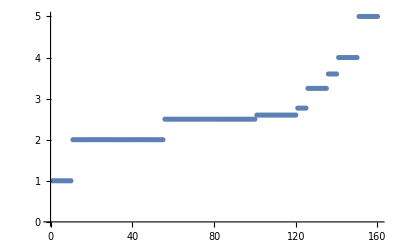

```mathematica
Table[((e[[1]]/e[[2]])/.repEmpty), {e,EdgeList[gr]}]//Sort//ListPlot
```

```mathematica
rep5Bis=Monitor[Table[ChangeSYmbol[allGraphs5[k,"colofourrealnull"]]-> allGraphs5[k,"atleast"],{k,Sort[allGraphs5NullAtomKeys]}],PadLeft[IntegerDigits[k,3],15]]
```

{n1x2x3x4x5→36,n1x2x3x45→13,n1x2x35x4→10,n1x2x34x5→13,n1x2x345→5,n1x25x3x4→10,n1x25x34→4,n1x24x3x5→10,n1x24x35→2,n1x245x3→4,n1x23x4x5→13,n1x23x45→5,n1x235x4→4,n1x234x5→5,n1x2345→2,n15x2x3x4→13,n15x2x34→5,n15x24x3→4,n15x23x4→5,n15x234→2,n14x2x3x5→10,n14x2x35→2,n14x25x3→2,n14x23x5→4,n14x235→1,n145x2x3→5,n145x23→2,n13x2x4x5→10,n13x2x45→4,n13x25x4→2,n13x24x5→2,n13x245→1,n135x2x4→4,n135x24→1,n134x2x5→4,n134x25→1,n1345x2→2,n12x3x4x5→13,n12x3x45→5,n12x35x4→4,n12x34x5→5,n12x345→2,n125x3x4→5,n125x34→2,n124x3x5→4,n124x35→1,n1245x3→2,n123x4x5→5,n123x45→2,n1235x4→2,n1234x5→2,n12345→1}

```mathematica
eq1=Simplify[Fold[And,Table[((e[[1]] >=e[[2]])/.rep5Bis), {e,EdgeList[gr]}]]]
```

True

```mathematica
eq2=Fold[
And,
Table[allGraphs5[k,"colofour"]≥ allGraphs5[k,"atleast"]
,{k,allGraphs5AtomKeys}]//Flatten
]
```

v1x2x3x4x5≥0&&v1x2x3x45≥0&&v1x2x35x4≥1&&v1x2x34x5≥0&&v1x2x345≥1&&v1x25x3x4≥1&&v1x25x34≥0&&v1x24x3x5≥1&&v1x24x35≥0&&v1x245x3≥0&&v1x23x4x5≥0&&v1x23x45≥1&&v1x235x4≥0&&v1x234x5≥1&&v1x2345≥1&&v15x2x3x4≥0&&v15x2x34≥1&&v15x24x3≥0&&v15x23x4≥1&&v15x234≥1&&v14x2x3x5≥1&&v14x2x35≥0&&v14x25x3≥0&&v14x23x5≥0&&v14x235≥0&&v145x2x3≥1&&v145x23≥1&&v13x2x4x5≥1&&v13x2x45≥0&&v13x25x4≥0&&v13x24x5≥0&&v13x245≥0&&v135x2x4≥0&&v135x24≥0&&v134x2x5≥0&&v134x25≥0&&v1345x2≥1&&v12x3x4x5≥0&&v12x3x45≥1&&v12x35x4≥0&&v12x34x5≥1&&v12x345≥1&&v125x3x4≥1&&v125x34≥1&&v124x3x5≥0&&v124x35≥0&&v1245x3≥1&&v123x4x5≥1&&v123x45≥1&&v1235x4≥1&&v1234x5≥1&&v12345≥1

```mathematica
Zero={alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key,K5Key}
```

{36166,31738,29608,36112,31714,29524}

```mathematica
eq3=Fold[
And,
Table[
allGraphs5[k,"colofour"]==0
,{k,Zero}]//Flatten
]
```

v13x24x5==0&&v14x25x3==0&&v1x24x35==0&&v13x25x4==0&&v14x2x35==0&&v1x2x3x4x5==0

```mathematica
(eq1&&eq2&&eq3//Simplify)/.rep5
```

-Graphics-295240==0&&-Graphics-295250≥0&&-Graphics-295271≥1&&-Graphics-295330≥0&&-Graphics-295371≥1&&-Graphics-295511≥1&&-Graphics-295600≥0&&-Graphics-296051≥1&&-Graphics-296080==0&&-Graphics-296330≥0&&-Graphics-297670≥0&&-Graphics-297681≥1&&-Graphics-297970≥0&&-Graphics-298571≥1&&-Graphics-298881≥1&&-Graphics-302530≥0&&-Graphics-302621≥1&&-Graphics-303340≥0&&-Graphics-304961≥1&&-Graphics-305861≥1&&-Graphics-317111≥1&&-Graphics-317140==0&&-Graphics-317380==0&&-Graphics-319540≥0&&-Graphics-319840≥0&&-Graphics-324411≥1&&-Graphics-326841≥1&&-Graphics-360851≥1&&-Graphics-360860≥0&&-Graphics-361120==0&&-Graphics-361660==0&&-Graphics-361940≥0&&-Graphics-368170≥0&&-Graphics-368980≥0&&-Graphics-382810≥0&&-Graphics-383080≥0&&-Graphics-390141≥1&&-Graphics-492070≥0&&-Graphics-492081≥1&&-Graphics-492100≥0&&-Graphics-492161≥1&&-Graphics-492201≥1&&-Graphics-499631≥1&&-Graphics-499721≥1&&-Graphics-514750≥0&&-Graphics-514780≥0&&-Graphics-522321≥1&&-Graphics-560111≥1&&-Graphics-560121≥1&&-Graphics-567701≥1&&-Graphics-582881≥1&&-Graphics-590481≥1

```mathematica
Simplify[
Fold[
And,
Table[allGraphs5[k,"colofour"]≥ allGraphs5[k,"atleast"]
,{k,Keys[allGraphs5]}]//Flatten
]
]
```

1
 |  |  |  |

```mathematica
long=Fold[
And,
Table[allGraphs5[k,"colofour"]≥ allGraphs5[k,"atleast"]
,{k,Keys[allGraphs5]}]//Flatten
]
```

1
 |  |  |  |

```mathematica
Length[long]
```

1895

```mathematica
Simplify[long]
```

1
 |  |  |  |

```mathematica
.
```

```mathematica
long=Fold[
And,
Table[Simplify[allGraphs5[k,"colofournull"]≥ allGraphs5[k,"atleast"]]
,{k,allGraphs5NullAtomKeys}]//Flatten
]
```

p1x2x3x4x5≥36&&p1x2x3x4x5≥13+p12x3x4x5&&p123x4x5+2 p1x2x3x4x5≥10+p12x3x4x5+p13x2x4x5+p1x23x4x5&&p123x4x5+p124x3x5+p12x34x5+p134x2x5+p13x24x5+p14x23x5+p1x234x5+6 p1x2x3x4x5≥p1234x5+2 (6+p12x3x4x5+p13x2x4x5+p14x2x3x5+p1x23x4x5+p1x24x3x5+p1x2x34x5)&&p12345+2 (p123x4x5+p124x3x5+p125x3x4+p12x34x5+p12x35x4+p12x3x45+p134x2x5+p135x2x4+p13x24x5+p13x25x4+p13x2x45+p145x2x3+p14x23x5+p14x25x3+p14x2x35+p15x23x4+p15x24x3+p15x2x34+p1x234x5+p1x235x4+p1x23x45+p1x245x3+p1x24x35+p1x25x34+p1x2x345+12 p1x2x3x4x5)≥24+p1234x5+p1235x4+p123x45+p1245x3+p124x35+p125x34+p12x345+6 p12x3x4x5+p1345x2+p134x25+p135x24+p13x245+6 p13x2x4x5+p145x23+p14x235+6 p14x2x3x5+p15x234+6 p15x2x3x4+p1x2345+6 p1x23x4x5+6 p1x24x3x5+6 p1x25x3x4+6 p1x2x34x5+6 p1x2x35x4+6 p1x2x3x45&&p123x4x5+p125x3x4+p12x35x4+p135x2x4+p13x25x4+p15x23x4+p1x235x4+6 p1x2x3x4x5≥p1235x4+2 (6+p12x3x4x5+p13x2x4x5+p15x2x3x4+p1x23x4x5+p1x25x3x4+p1x2x35x4)&&p123x4x5+p12x3x45+p13x2x45+p1x23x45+2 p1x2x3x4x5≥4+p123x45+p12x3x4x5+p13x2x4x5+p1x23x4x5+2 p1x2x3x45&&p124x3x5+2 p1x2x3x4x5≥8+p12x3x4x5+p14x2x3x5+p1x24x3x5&&p124x3x5+p125x3x4+p12x3x45+p145x2x3+p14x25x3+p15x24x3+p1x245x3+6 p1x2x3x4x5≥p1245x3+2 (6+p12x3x4x5+p14x2x3x5+p15x2x3x4+p1x24x3x5+p1x25x3x4+p1x2x3x45)&&p124x3x5+p12x35x4+p14x2x35+p1x24x35+2 p1x2x3x4x5≥2+p124x35+p12x3x4x5+p14x2x3x5+p1x24x3x5+2 p1x2x35x4&&p125x3x4+2 p1x2x3x4x5≥10+p12x3x4x5+p15x2x3x4+p1x25x3x4&&p125x3x4+p12x34x5+p15x2x34+p1x25x34+2 p1x2x3x4x5≥4+p125x34+p12x3x4x5+p15x2x3x4+p1x25x3x4+2 p1x2x34x5&&p12x34x5+p1x2x3x4x5≥5+p12x3x4x5+p1x2x34x5&&p12x34x5+p12x35x4+p12x3x45+p1x2x345+2 p1x2x3x4x5≥4+p12x345+2 p12x3x4x5+p1x2x34x5+p1x2x35x4+p1x2x3x45&&p12x35x4+p1x2x3x4x5≥4+p12x3x4x5+p1x2x35x4&&p12x3x45+p1x2x3x4x5≥5+p12x3x4x5+p1x2x3x45&&p1x2x3x4x5≥10+p13x2x4x5&&p134x2x5+2 p1x2x3x4x5≥8+p13x2x4x5+p14x2x3x5+p1x2x34x5&&p134x2x5+p135x2x4+p13x2x45+p145x2x3+p14x2x35+p15x2x34+p1x2x345+6 p1x2x3x4x5≥p1345x2+2 (6+p13x2x4x5+p14x2x3x5+p15x2x3x4+p1x2x34x5+p1x2x35x4+p1x2x3x45)&&p134x2x5+p13x25x4+p14x25x3+p1x25x34+2 p1x2x3x4x5≥2+p134x25+p13x2x4x5+p14x2x3x5+2 p1x25x3x4+p1x2x34x5&&p135x2x4+2 p1x2x3x4x5≥8+p13x2x4x5+p15x2x3x4+p1x2x35x4&&p135x2x4+p13x24x5+p15x24x3+p1x24x35+2 p1x2x3x4x5≥2+p135x24+p13x2x4x5+p15x2x3x4+2 p1x24x3x5+p1x2x35x4&&p13x24x5+p1x2x3x4x5≥2+p13x2x4x5+p1x24x3x5&&p13x24x5+p13x25x4+p13x2x45+p1x245x3+2 p1x2x3x4x5≥2+p13x245+2 p13x2x4x5+p1x24x3x5+p1x25x3x4+p1x2x3x45&&p13x25x4+p1x2x3x4x5≥2+p13x2x4x5+p1x25x3x4&&p13x2x45+p1x2x3x4x5≥4+p13x2x4x5+p1x2x3x45&&p1x2x3x4x5≥10+p14x2x3x5&&p145x2x3+2 p1x2x3x4x5≥10+p14x2x3x5+p15x2x3x4+p1x2x3x45&&p145x2x3+p14x23x5+p15x23x4+p1x23x45+2 p1x2x3x4x5≥4+p145x23+p14x2x3x5+p15x2x3x4+2 p1x23x4x5+p1x2x3x45&&p14x23x5+p1x2x3x4x5≥4+p14x2x3x5+p1x23x4x5&&p14x23x5+p14x25x3+p14x2x35+p1x235x4+2 p1x2x3x4x5≥2+p14x235+2 p14x2x3x5+p1x23x4x5+p1x25x3x4+p1x2x35x4&&p14x25x3+p1x2x3x4x5≥2+p14x2x3x5+p1x25x3x4&&p14x2x35+p1x2x3x4x5≥2+p14x2x3x5+p1x2x35x4&&p1x2x3x4x5≥13+p15x2x3x4&&p15x23x4+p1x2x3x4x5≥5+p15x2x3x4+p1x23x4x5&&p15x23x4+p15x24x3+p15x2x34+p1x234x5+2 p1x2x3x4x5≥4+p15x234+2 p15x2x3x4+p1x23x4x5+p1x24x3x5+p1x2x34x5&&p15x24x3+p1x2x3x4x5≥4+p15x2x3x4+p1x24x3x5&&p15x2x34+p1x2x3x4x5≥5+p15x2x3x4+p1x2x34x5&&p1x2x3x4x5≥13+p1x23x4x5&&p1x234x5+2 p1x2x3x4x5≥10+p1x23x4x5+p1x24x3x5+p1x2x34x5&&p1x234x5+p1x235x4+p1x23x45+p1x245x3+p1x24x35+p1x25x34+p1x2x345+6 p1x2x3x4x5≥p1x2345+2 (6+p1x23x4x5+p1x24x3x5+p1x25x3x4+p1x2x34x5+p1x2x35x4+p1x2x3x45)&&p1x235x4+2 p1x2x3x4x5≥8+p1x23x4x5+p1x25x3x4+p1x2x35x4&&p1x23x45+p1x2x3x4x5≥5+p1x23x4x5+p1x2x3x45&&p1x2x3x4x5≥10+p1x24x3x5&&p1x245x3+2 p1x2x3x4x5≥8+p1x24x3x5+p1x25x3x4+p1x2x3x45&&p1x24x35+p1x2x3x4x5≥2+p1x24x3x5+p1x2x35x4&&p1x2x3x4x5≥10+p1x25x3x4&&p1x25x34+p1x2x3x4x5≥4+p1x25x3x4+p1x2x34x5&&p1x2x3x4x5≥13+p1x2x34x5&&p1x2x345+2 p1x2x3x4x5≥10+p1x2x34x5+p1x2x35x4+p1x2x3x45&&p1x2x3x4x5≥10+p1x2x35x4&&p1x2x3x4x5≥13+p1x2x3x45

```mathematica
Simplify[long]
```

p1x2x3x4x5≥36&&p1x2x3x4x5≥13+p12x3x4x5&&p123x4x5+2 p1x2x3x4x5≥10+p12x3x4x5+p13x2x4x5+p1x23x4x5&&p123x4x5+p124x3x5+p12x34x5+p134x2x5+p13x24x5+p14x23x5+p1x234x5+6 p1x2x3x4x5≥p1234x5+2 (6+p12x3x4x5+p13x2x4x5+p14x2x3x5+p1x23x4x5+p1x24x3x5+p1x2x34x5)&&p12345+2 (p123x4x5+p124x3x5+p125x3x4+p12x34x5+p12x35x4+p12x3x45+p134x2x5+p135x2x4+p13x24x5+p13x25x4+p13x2x45+p145x2x3+p14x23x5+p14x25x3+p14x2x35+p15x23x4+p15x24x3+p15x2x34+p1x234x5+p1x235x4+p1x23x45+p1x245x3+p1x24x35+p1x25x34+p1x2x345+12 p1x2x3x4x5)≥24+p1234x5+p1235x4+p123x45+p1245x3+p124x35+p125x34+p12x345+6 p12x3x4x5+p1345x2+p134x25+p135x24+p13x245+6 p13x2x4x5+p145x23+p14x235+6 p14x2x3x5+p15x234+6 p15x2x3x4+p1x2345+6 p1x23x4x5+6 p1x24x3x5+6 p1x25x3x4+6 p1x2x34x5+6 p1x2x35x4+6 p1x2x3x45&&p123x4x5+p125x3x4+p12x35x4+p135x2x4+p13x25x4+p15x23x4+p1x235x4+6 p1x2x3x4x5≥p1235x4+2 (6+p12x3x4x5+p13x2x4x5+p15x2x3x4+p1x23x4x5+p1x25x3x4+p1x2x35x4)&&p123x4x5+p12x3x45+p13x2x45+p1x23x45+2 p1x2x3x4x5≥4+p123x45+p12x3x4x5+p13x2x4x5+p1x23x4x5+2 p1x2x3x45&&p124x3x5+2 p1x2x3x4x5≥8+p12x3x4x5+p14x2x3x5+p1x24x3x5&&p124x3x5+p125x3x4+p12x3x45+p145x2x3+p14x25x3+p15x24x3+p1x245x3+6 p1x2x3x4x5≥p1245x3+2 (6+p12x3x4x5+p14x2x3x5+p15x2x3x4+p1x24x3x5+p1x25x3x4+p1x2x3x45)&&p124x3x5+p12x35x4+p14x2x35+p1x24x35+2 p1x2x3x4x5≥2+p124x35+p12x3x4x5+p14x2x3x5+p1x24x3x5+2 p1x2x35x4&&p125x3x4+2 p1x2x3x4x5≥10+p12x3x4x5+p15x2x3x4+p1x25x3x4&&p125x3x4+p12x34x5+p15x2x34+p1x25x34+2 p1x2x3x4x5≥4+p125x34+p12x3x4x5+p15x2x3x4+p1x25x3x4+2 p1x2x34x5&&p12x34x5+p1x2x3x4x5≥5+p12x3x4x5+p1x2x34x5&&p12x34x5+p12x35x4+p12x3x45+p1x2x345+2 p1x2x3x4x5≥4+p12x345+2 p12x3x4x5+p1x2x34x5+p1x2x35x4+p1x2x3x45&&p12x35x4+p1x2x3x4x5≥4+p12x3x4x5+p1x2x35x4&&p12x3x45+p1x2x3x4x5≥5+p12x3x4x5+p1x2x3x45&&p1x2x3x4x5≥10+p13x2x4x5&&p134x2x5+2 p1x2x3x4x5≥8+p13x2x4x5+p14x2x3x5+p1x2x34x5&&p134x2x5+p135x2x4+p13x2x45+p145x2x3+p14x2x35+p15x2x34+p1x2x345+6 p1x2x3x4x5≥p1345x2+2 (6+p13x2x4x5+p14x2x3x5+p15x2x3x4+p1x2x34x5+p1x2x35x4+p1x2x3x45)&&p134x2x5+p13x25x4+p14x25x3+p1x25x34+2 p1x2x3x4x5≥2+p134x25+p13x2x4x5+p14x2x3x5+2 p1x25x3x4+p1x2x34x5&&p135x2x4+2 p1x2x3x4x5≥8+p13x2x4x5+p15x2x3x4+p1x2x35x4&&p135x2x4+p13x24x5+p15x24x3+p1x24x35+2 p1x2x3x4x5≥2+p135x24+p13x2x4x5+p15x2x3x4+2 p1x24x3x5+p1x2x35x4&&p13x24x5+p1x2x3x4x5≥2+p13x2x4x5+p1x24x3x5&&p13x24x5+p13x25x4+p13x2x45+p1x245x3+2 p1x2x3x4x5≥2+p13x245+2 p13x2x4x5+p1x24x3x5+p1x25x3x4+p1x2x3x45&&p13x25x4+p1x2x3x4x5≥2+p13x2x4x5+p1x25x3x4&&p13x2x45+p1x2x3x4x5≥4+p13x2x4x5+p1x2x3x45&&p1x2x3x4x5≥10+p14x2x3x5&&p145x2x3+2 p1x2x3x4x5≥10+p14x2x3x5+p15x2x3x4+p1x2x3x45&&p145x2x3+p14x23x5+p15x23x4+p1x23x45+2 p1x2x3x4x5≥4+p145x23+p14x2x3x5+p15x2x3x4+2 p1x23x4x5+p1x2x3x45&&p14x23x5+p1x2x3x4x5≥4+p14x2x3x5+p1x23x4x5&&p14x23x5+p14x25x3+p14x2x35+p1x235x4+2 p1x2x3x4x5≥2+p14x235+2 p14x2x3x5+p1x23x4x5+p1x25x3x4+p1x2x35x4&&p14x25x3+p1x2x3x4x5≥2+p14x2x3x5+p1x25x3x4&&p14x2x35+p1x2x3x4x5≥2+p14x2x3x5+p1x2x35x4&&p1x2x3x4x5≥13+p15x2x3x4&&p15x23x4+p1x2x3x4x5≥5+p15x2x3x4+p1x23x4x5&&p15x23x4+p15x24x3+p15x2x34+p1x234x5+2 p1x2x3x4x5≥4+p15x234+2 p15x2x3x4+p1x23x4x5+p1x24x3x5+p1x2x34x5&&p15x24x3+p1x2x3x4x5≥4+p15x2x3x4+p1x24x3x5&&p15x2x34+p1x2x3x4x5≥5+p15x2x3x4+p1x2x34x5&&p1x2x3x4x5≥13+p1x23x4x5&&p1x234x5+2 p1x2x3x4x5≥10+p1x23x4x5+p1x24x3x5+p1x2x34x5&&p1x234x5+p1x235x4+p1x23x45+p1x245x3+p1x24x35+p1x25x34+p1x2x345+6 p1x2x3x4x5≥p1x2345+2 (6+p1x23x4x5+p1x24x3x5+p1x25x3x4+p1x2x34x5+p1x2x35x4+p1x2x3x45)&&p1x235x4+2 p1x2x3x4x5≥8+p1x23x4x5+p1x25x3x4+p1x2x35x4&&p1x23x45+p1x2x3x4x5≥5+p1x23x4x5+p1x2x3x45&&p1x2x3x4x5≥10+p1x24x3x5&&p1x245x3+2 p1x2x3x4x5≥8+p1x24x3x5+p1x25x3x4+p1x2x3x45&&p1x24x35+p1x2x3x4x5≥2+p1x24x3x5+p1x2x35x4&&p1x2x3x4x5≥10+p1x25x3x4&&p1x25x34+p1x2x3x4x5≥4+p1x25x3x4+p1x2x34x5&&p1x2x3x4x5≥13+p1x2x34x5&&p1x2x345+2 p1x2x3x4x5≥10+p1x2x34x5+p1x2x35x4+p1x2x3x45&&p1x2x3x4x5≥10+p1x2x35x4&&p1x2x3x4x5≥13+p1x2x3x45

```mathematica
%==long
```

True